Given the scalar valued functions K>0 and T, there is a unique curve, up to isometry, with curvature K and torsion T.  This notebook approximates these curves.

In the 3d case, for example, at each step we have a pt, a tangent, a normal and bi-normal.
We change these by:
	next pt= old pt + stepsize* tan
	next tan= old tan + stepsize * K * norm  
	next norm = old norm + stepsize * (-K) * tan + stepsize * (T) * binorm
	next binorm = next tan X next norm  (or equivalently, = old binorm + stepsize (-T) norm)
	
	Stepsize must be fairly small in order for this to work well (clearly, an infinitessimal stepsize is best)

### 2D

```mathematica
steptan[{tan_,pt_,t_},k_,stepsize_]:=
	{tan+ stepsize k[t] {-tan[[2]],tan[[1]]}, pt+ tan stepsize, t+stepsize}
```

```mathematica
PlotCurvature[k_,{tmin_,tmax_},stepsize_,opts___]:=

Show[Graphics[Line[ (#[[2]]&/@
	
		NestList[steptan[#,k,stepsize]&, {{1,0},{0,0},tmin},
			Floor[(tmax-tmin)/stepsize]] )],opts]]
```

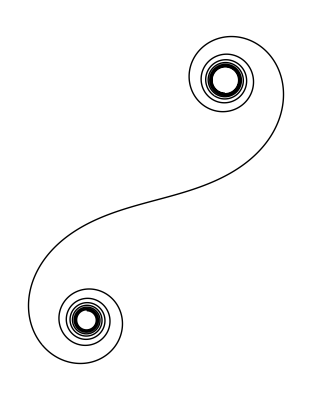

```mathematica
PlotCurvature[#&,{-10,10},.001,Axes->False,AspectRatio->Automatic]
```

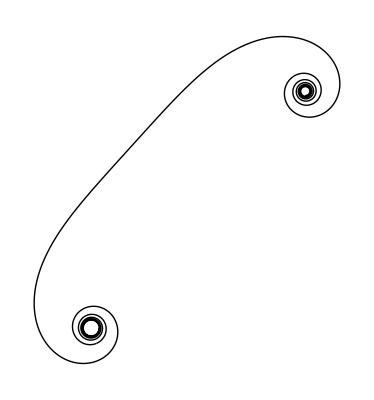

```mathematica
PlotCurvature[#^2 &,{-5,5},.001,Axes->False,AspectRatio->Automatic]
```

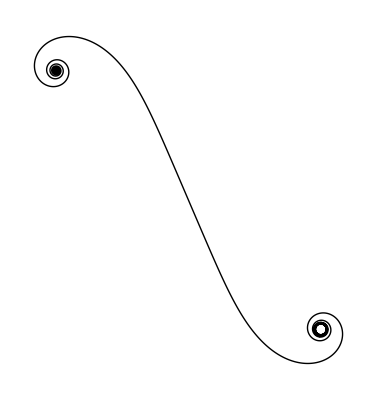

```mathematica
PlotCurvature[#^3 &,{-4,4},.001,Axes->False,AspectRatio->Automatic]
```

### 3D

```mathematica
(*Cross[	{a_,b_,c_},
		{d_,e_,f_}]:=
	{b f - c e, c d - a f, a e- b d}*) (*Later added to Mathemamatica natively*)
```

```mathematica
steptan3D[{tan_,norm_,pt_,t_},k_,tor_,stepsize_]:=
	{tan+ stepsize k[t] norm, 
	norm + (-k[t]) stepsize tan + tor[t] stepsize Cross[tan,norm],
	pt+ tan stepsize, t+stepsize} //N
```

```mathematica
PlotCurvature3D[k_,tor_,{tmin_,tmax_},stepsize_,opts___]:=

Show[Graphics3D[{Thick, Red, Line[ (#[[3]]&/@
	
		NestList[steptan3D[#,k,tor,stepsize]&, {{1,0,0},{0,1,0},{0,0,0},tmin},
			Floor[(tmax-tmin)/stepsize]] )]},opts]]
```

```mathematica
?Graphics3D
```

RowBox[{"Graphics3D", "[", RowBox[{StyleBox["primitives", "TI"], ",", StyleBox["options", "TI"]}], "]"}] represents a three-dimensional graphical image.

```mathematica
tor[t_]:=5;
kurv[t_]:=10;
PlotCurvature3D[kurv,tor,{0,1},.01,Axes->False,AspectRatio->Automatic,Boxed->False]]
```

-Graphics3D-

```mathematica
kurv[t_]:=10;
tor[t_]:=20t;
PlotCurvature3D[kurv,tor,{0,1},.001,Axes->False,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
kurv[t_]:=10;
tor[t_]:=50t^2;
PlotCurvature3D[kurv,tor,{-1,1},.001,Axes->False,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
kurv[t_]:= t^2;
tor[t_]:=1;
PlotCurvature3D[kurv,tor,{-6,6},.001,Axes->False,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
kurv[t_]:= 3;
tor[t_]:=t;
PlotCurvature3D[kurv,tor,{-6,6},.001,Axes->False,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
kurv[t_]:= Abs[t];
tor[t_]:=t;
PlotCurvature3D[kurv,tor,{-6,6},.001,Axes->False,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
PlotCurvature3D[kurv,tor,{-6,6},.001,Axes->False,AspectRatio->Automatic]
```